# xCellerator Example

ring-oscillator-michaelis-single-stage.nb

## A ring oscillator based on single-stage michaelis-menten reactions

Created: 02 August 2005 BES
Revised: 15 Oct 2007 (BES) To work with M6.0

```mathematica
<<xlr8r.m
```

xlr8r 0.60 (15-Oct-2007) loaded 15-October-2007 14:59:26.744987 using Mathematica 6.0 for Mac OS X x86 (32-bit) (June 19, 2007)

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {XP,YP,ZP}

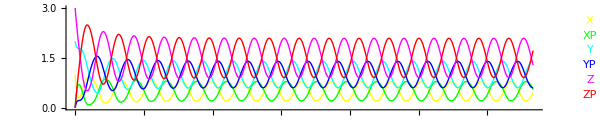

```mathematica
reactions={{Underoverscript[X⟺XP, ZP, Z],MM[K,v,K,v]}, {Underoverscript[Y⟺YP, XP, X],MM[K,v,K,v]},
{Underoverscript[Z⟺ZP, YP, Y],MM[K,v,K,v]}};odes=interpret[reactions];
r=run[odes, timeSpan-> 100,initialConditions-> {X-> 1, Y-> 2, Z-> 3}, rates-> {v-> 1, K-> .5}];
runPlot[r,PlotRange-> All, ImageSize-> 600, AspectRatio-> 0.2]
```

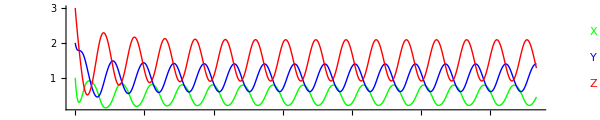

```mathematica
runPlot[r,{X,Y,Z},PlotRange-> All, ImageSize-> 600, AspectRatio-> 0.2]
```

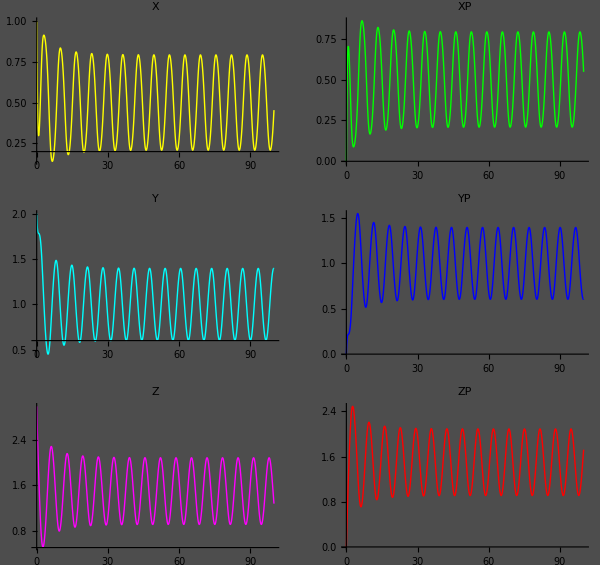

```mathematica
g=gridPlot[r, All, {0,100}, plotColumns-> 2, ImageSize-> 600, Background-> GrayLevel[0.3]]
```